```mathematica
a=0.1;b=0.05;f1[k_]:=Sqrt[a^2+b^2+Sqrt[2 a^2 b^2 (1+Cos[2 k])]];f2[k_]:=Sqrt[a^2+b^2-Sqrt[2 a^2 b^2 (1+Cos[2 k])]];f3[k_]:=Sqrt[a^2+b^2+2 a b Cos[k]];
```

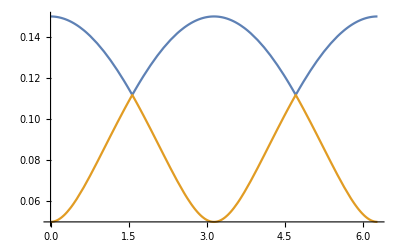

```mathematica
Plot[{f1[k],f2[k]},{k,0,2Pi}]
```

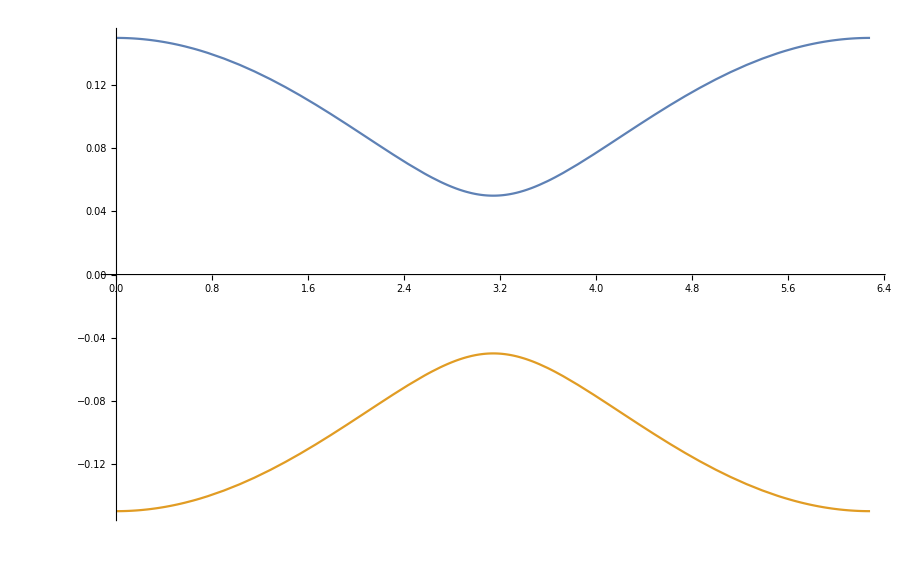

```mathematica
Plot[{f3[k],-f3[k]},{k,0,2Pi}]
```

```mathematica
Clear[b]
```

```mathematica
Integrate[Sqrt[a^2+b^2+2 a b Cos[k]],k]
```

(2 √(a^2+b^2+2 a b Cos[k]) EllipticE[k/2,(4 a b)/(a+b)^2])/(√((a^2+b^2+2 a b Cos[k])/(a+b)^2))

```mathematica
f[k_]:=(2 √(a^2+b^2+2 a b Cos[k]) EllipticE[k/2,(4 a b)/(a+b)^2])/(√((a^2+b^2+2 a b Cos[k])/(a+b)^2));
```

```mathematica
f[2 Pi]
```

(4 √(a^2+2 a b+b^2) EllipticE[(4 a b)/(a+b)^2])/(√((a^2+2 a b+b^2)/(a+b)^2))

```mathematica
FullSimplify[f[2 Pi]-f[0]]
```

4 √((a+b)^2) EllipticE[(4 a b)/(a+b)^2]

```mathematica
a=-0.7;b=0.69;
```

```mathematica
bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;
```

```mathematica
En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;
```

```mathematica
sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}]
```

{t→0.307079,lambda→0.329475}

```mathematica
t0=Last[First[sol]]
```

0.307079

```mathematica
lambda0=Last[Last[sol]]
```

0.329475

```mathematica
disp[k_]:=Sqrt[(1-2(1+a)t0)^2+(b (1+2(1+a)lambda0))^2+2 (1-2(1+a)t0) (b (1+2(1+a)lambda0)) Cos[k]];
```

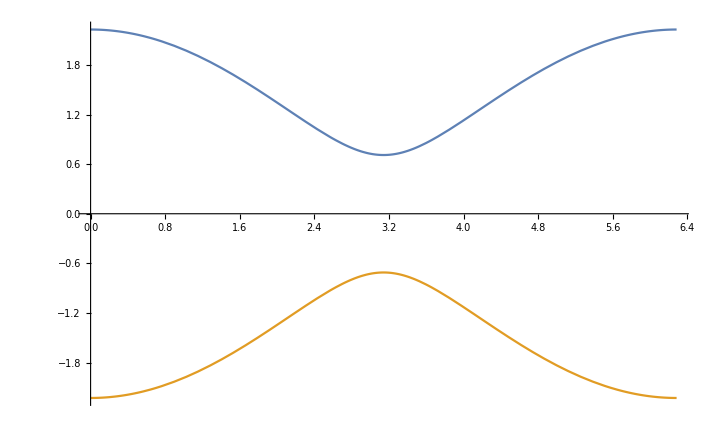

```mathematica
Plot[{disp[k],-disp[k]},{k,0,2Pi}]
```

```mathematica
gap=2 disp[Pi]
```

0.0212998

```mathematica
Clear[gap]
```

```mathematica
amin=-0.99;amax=-0.01;bmin=0.01;bmax=1.0;ngrid=10;For[i=0,i≤ngrid,i++,For[j=0,j≤ngrid,j++,a=amin+i/ngrid*(amax-amin);b=bmin+j/ngrid*(bmax-bmin);bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}];t0=Last[First[sol]];lambda0=Last[Last[sol]];disp[k_]:=Sqrt[(1-2(1+a)t0)^2+(b (1+2(1+a)lambda0))^2+2 (1-2(1+a)t0) (b (1+2(1+a)lambda0)) Cos[k]];gap[i][j]=2 disp[Pi]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

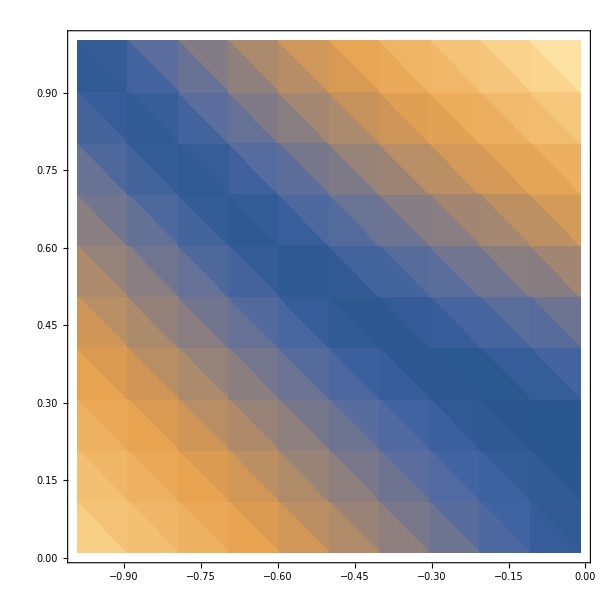

```mathematica
ListDensityPlot[Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1],InterpolationOrder->1]
```

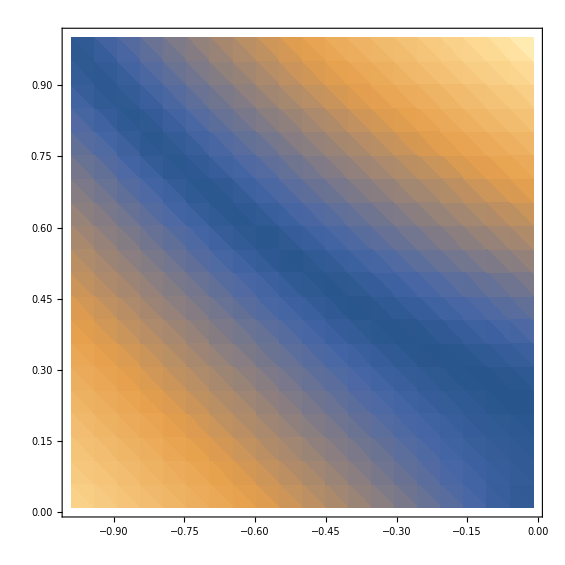

```mathematica
ListPlot3D[Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1]]
```

-Graphics3D-

-Graphics3D-

```mathematica
a=-0.1;b=0.8;
```

```mathematica
bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}];t0=Last[First[sol]];lambda0=Last[Last[sol]];
```

```mathematica
t0
```

0.13394

```mathematica
lambda0
```

0.464764

```mathematica
Plot3D[En[t,lambda],{t,-0.5,0.5},{lambda,-0.7,0.7}]
```

-Graphics3D-